```mathematica
Clear["`*"]
```

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Concatenate
```

# Physics 471 - Optics

## Equations

Fresnel Coefficients

```mathematica
α[θ1_,θ2_]:= Cos[θ2]/Cos[θ1]
β[n1_,n2_]:=n2/n1
ts[α_,β_]:=2/(1+α *β)
tp[α_,β_]:= 2/(α+β)
rs[α_,β_]:= (1-α β)/(1+α β)
rp[α_,β_]:= (α-β)/(α+β)
```

## Homework

## 1 - Due 1-10-12

```mathematica
VectorAngle[{1,2,-3},{-1,3,2}]*180./π
```

94.096

## 2 - Due 1-12-12

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
Curl[{7 Xx^2*Yy^3,2 Zz^4,0}*Cos[ω*t]]
```

{-8 Zz^3 cos(t ω),0,-21 Xx^2 Yy^2 cos(t ω)}

```mathematica
Laplacian[7 Xx^2*Yy^3,2 Zz^4,0]
```

Laplacian(7 Xx^2 Yy^3,2 Zz^4,0)

### P 1.11

```mathematica
radiusOfEarthOrbit = 1.5*10^11
timeOfOrbit = 365*24
periodOfIo = 42.5
```

1.5×10^11

8760

42.5

```mathematica
speedOfEarth = (2*π*radiusOfEarthOrbit)/timeOfOrbit
```

1.07589×10^8

```mathematica
distanceIn40Periods=speedOfEarth*42.5*40
```

1.82901×10^11

```mathematica
distanceIn40Periods/(3*^8)*1/60
```

10.1612

```mathematica
%*2
```

20.3223

```mathematica
22*60
```

1320

```mathematica
(distanceIn40Periods*2)/1320
```

2.77123×10^8

### Lab

```mathematica
x1 = 1.95;
x2 = 2.07;
x3= 2.08;
x4 =41.7;
x5 = .75;
cwω = 465;
ccwω = 555;
d = 0.0102;
distanceLightTravels = 2*(x3+x4+x5)
angleRotated = d/((x1+x2)*2)
angularVelocity = 2.0π*cwω
timeTakenToTravel = angleRotated/angularVelocity
(*FINAL ANSWER *)distanceLightTravels/timeTakenToTravel
```

89.06

0.00126866

2921.68

4.34221×10^-7

2.05103×10^8

## 3 - Due 1-17-12

```mathematica
D[e*Cos[k*(ux*rx+uy*ry+uz*rz-c*t)+ϕ],{t,2}]//TraditionalForm
```

-c^2 e k^2 cos(k (-c t+rx ux+ry uy+rz uz)+ϕ)

```mathematica
{a,b,c}^2
```

{a^2,b^2,c^2}

```mathematica
z1 = 1-I
z2 = 3+4*I
Arg[z1]
Arg[z2]//N
(7π/4-Arg[z2])*(180./π)//N
z1/z2
```

1-ⅈ

3+4 ⅈ

-π/4

0.927295

261.87

-1/25-(7 ⅈ)/25

```mathematica
TrigToExp[a*Cos[ω*t]]//Simplify
TrigToExp[2*a*Sin[ω*t+π/4]]
```

1/2 a ⅇ^(-ⅈ t ω) (1+ⅇ^(2 ⅈ t ω))

ⅈ a ⅇ^(-(ⅈ π)/4-ⅈ t ω)-ⅈ a ⅇ^((ⅈ π)/4+ⅈ t ω)

```mathematica
Tan[4.57049]
```

6.9999

261.87

```mathematica
(ArcTan[-5/-2]+π)*180./π
```

248.199

```mathematica
π/2.
```

1.5708

```mathematica
a*Cos[ω*t]//ComplexExpand
```

a Cos[t ω]

## 4 - Due 1-19-12

### Colton 3:

```mathematica
(3.83+0.2*I)^2
```

14.6289+1.532 ⅈ

```mathematica
Solve[3.86+0.2*I==√(1+x),x]
```

{{x→13.8596+1.544 ⅈ}}

### P2.2:

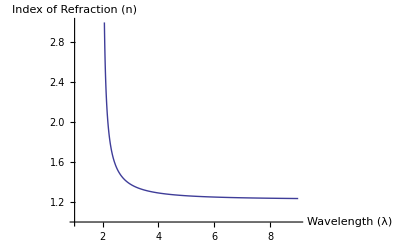

```mathematica
Plot[{√(1+(.5*x^2)/(x^2-(200*^-9)^2))},{x,100*^-9,900*^-9},PlotRange->{1,3},AxesLabel->{"Wavelength (λ)","Index of Refraction (n)"}]
```

### P 2.3:

```mathematica
n = 10*^28;
ω0 = 6*^15;
γ = ω0/5;
E0 = 10^4;
w1 = ω0-2*γ;
w2 = ω0;
w3 = ω0 +2*γ;
q = 1.60217646*^-19;
m = 9.10938188*^-31;
```

#### a.) find phase and amplitude for r_micro

```mathematica
phaseA [ω_]:= ArcTan[(ω*γ)/(ω0^2-ω^2)]
ampA[ω_]:=(q*E0)/m*1/(√((ω0^2-ω^2)+(ω*γ)^2))
```

```mathematica
phaseA/@{w1,w2,w3}//N
ampA /@{w1,w2,w3}//N
```

Power::infy: Infinite expression TraditionalForm`1/0 encountered.

{0.185348,Indeterminate,-0.283794}

{4.07134×10^-16,2.44281×10^-16,1.74486×10^-16}

#### b.) find the phase and amplitude for P(ω)

#### c.) find phase and amplitude for χ(ω) (also find it for 2*E0)

#### d.) Find n and κ at w0, w1, w2.

#### e.) find the three speeds of light in terms of c. Find the three wavelengths λ

#### f.) Find how far light penetrates into the material before only 1/e of the amplitude of E remains. Find how far light penetrates into the material before only 1/e of the intensity I remains.

## 5 - Due 1-24-12

### 2.6

```mathematica
q = 1.60217646*^-19;
m = 9.10938188*^-31;
e0 = 8.8542*^-12;
n = 5.68*^28;
λ = 633*^-9;
σ = 6.62*^7;
wp = √((n q^2)/(e0 m))
w = 2π (3*^8)/λ//N
γ = (n q^2)/(m σ)
```

1.34451×10^16

2.97781×10^15

2.41781×10^13

```mathematica
χ = -wp^2/(I*w*γ+w^2)
```

-20.3848+0.165513 ⅈ

```mathematica
Ν = √(1+χ)
```

0.0187961+4.40286 ⅈ

### 2.7

#### a.)

```mathematica
w7 = 100*^6 * 2 π;
```

```mathematica
n7 = (1-(.9)^2)*((e0 m w7^2)/q^2)
```

2.35684×10^13

#### b.)

```mathematica
w7b = 1160*^3*2*π;
```

```mathematica
Ν7 = √(1-(n7*q^2)/(e0*m*w7b^2))
```

0.+37.5634 ⅈ

### 2.8

```mathematica
wp28 = 1;
γ28 = 0.02wp28;
func[w28_] := √(1-wp28^2/(I*γ28*w28+w28^2))
```

```mathematica
Expand[ComplexExpand[func[x]]]//Simplify//StandardForm
```

((0.0004 x^2+0.9992 x^4-1.9992 x^6+x^8)/((0.+0.0004 x^2+x^4)^2))^(1/4) (Cos[0.5 Arg[1.-1./((0.+0.02 ⅈ) x+x^2)]]+ⅈ Sin[0.5 Arg[1.-1./((0.+0.02 ⅈ) x+x^2)]])

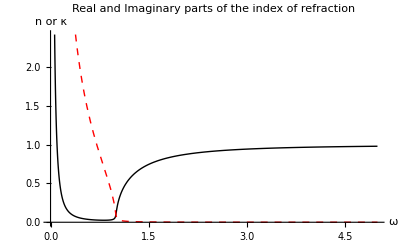

```mathematica
Plot[{((0.0004 x^2+0.9992001600000001 x^4-1.9992 x^6+x^8)/((0.+0.0004 x^2+x^4)^2))^(1/4) *Cos[0.5 Arg[1.-1./((0.+0.02 ⅈ) x+x^2)]],((0.0004 x^2+0.9992001600000001 x^4-1.9992 x^6+x^8)/((0.+0.0004 x^2+x^4)^2))^(1/4)Sin[0.5 Arg[1.-1./((0.+0.02 ⅈ) x+x^2)]]},{x,0,5},PlotLabel->"Real and Imaginary parts of the index of refraction",AxesLabel->{"ω","n or κ"},PlotStyle->{{Thick,Black},{Dashed,Thick,Red}}]
```

## 6 - Due 1-26-12

### 2.10

```mathematica
n = 1; e0 = 8.8542*^-12;q = 1.60217646*^-19;m = 9.10938188*^-31; c = 3*^8;μ0 = 4 π *10^-7 (* T m/A *);
```

#### a.)

```mathematica
energy = 100*^-3;
raduis = 5*^-6;
time = 2.5*^-14;
intensity  = (energy/time)/(π*raduis^2)
```

5.09296×10^22

#### b.)

```mathematica
efield=√(2*intensity/(1*e0 c))
```

6.19248×10^12

#### c.)

```mathematica
bfield = efield/c
```

20641.6

### 3.3

```mathematica
ni = 1; nt = 1.6;θ2 = ArcSin[ni/nt Sin[θi]];
```

```mathematica
rs=(ni Cos[θi]-nt * Cos[θ2])/(ni Cos[θi]+nt *Cos[θ2]);
ts=(2 ni Cos[θi])/(ni Cos[θi]+nt Cos[θ2]);
Rs=Abs[rs]^2;
Ts=1-Rs;
rp=(ni Cos[θ2] - nt Cos[θi])/(ni Cos[θ2] + nt Cos[θi]);
tp=(2 ni Cos[θi])/(ni Cos[θ2]  + nt Cos[θi]);
Rp=Abs[rp]^2;
Tp=1-Rp;
```

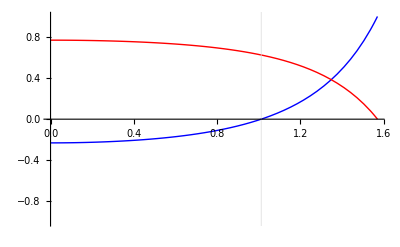

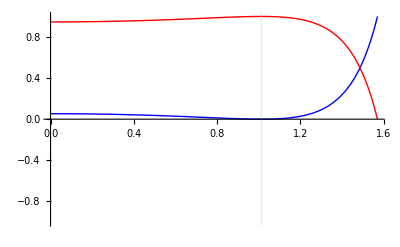

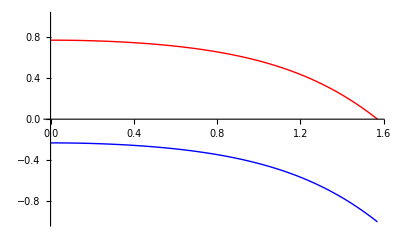

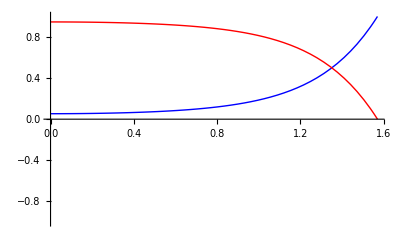

```mathematica
Plot[{rp,tp},{θi,0,π/2},PlotRange->{-1,1},PlotStyle->{{Blue,Thick},{Red,Thick}},PlotLegend->{"r_p","t_p"},GridLines->{{ArcTan[nt/ni]},{}}]
Plot[{Rp,Tp},{θi,0,π/2},PlotRange->{-1,1},PlotStyle->{{Blue,Thick},{Red,Thick}},PlotLegend->{"R_p","T_p"},GridLines->{{ArcTan[nt/ni]},{}}]
Plot[{rs,ts},{θi,0,π/2},PlotRange->{-1,1},PlotStyle->{{Blue,Thick},{Red,Thick}},PlotLegend->{"r_s","t_s"}]
Plot[{Rs,Ts},{θi,0,π/2},PlotRange->{-1,1},PlotStyle->{{Blue,Thick},{Red,Thick}},PlotLegend->{"R_s","T_s"}]
```

### L3.4

NOTE FOR THIS PROBLEM THE DETECTOR GAVE OUT POWER, BUT POWER AND INTENSITY ARE DIRECTLY PROPORTIONAL SO NO CONVERSION WAS NEEDED.

```mathematica
sData = {sangle,sPower} = Transpose[({{Start, 2.614}, {5, .105}, {10, .104}, {15, .111}, {20, .118}, {25, .132}, {30, .152}, {35, .177}, {40, .206}, {45, .249}, {50, .304}, {55, .3595}, {60, .458}, {65, .604}, {70, .799}, {75, 1.005}, {80, 1.429}})];
```

```mathematica
pData ={pAngle,sAngle}= Transpose[({{Start, .313}, {5, .01275}, {10, .01195}, {15, .01121}, {20, .01489}, {25, .00912}, {30, .00796}, {35, .00605}, {40, .00428}, {45, .00239}, {50, .00097}, {55, .0000967}, {60, .00084}, {65, .00583}, {70, .01339}, {75, .02781}, {80, .0597}})];
```

```mathematica
pReflectance = pData[[2]]/pData[[2,1]];
sReflectance = sData[[2]]/sData[[2,1]];
titles = {"Angle","Power","Reflectance"};
pAnswer = Insert[Transpose[{pData[[1]],pData[[2]],pReflectance}],titles,1]//TableView
sAnswer = Insert[Transpose[{sData[[1]],sData[[2]],sReflectance}],titles,1]//TableView
```

```mathematica
{{, "Angle", "Power", "Reflectance"}, {1, Start (p polarized), 0.313, 1.}, {2, 5, 0.01275, 0.0407348}, {3, 10, 0.01195, 0.0381789}, {4, 15, 0.01121, 0.0358147}, {5, 20, 0.01489, 0.0475719}, {6, 25, 0.00912, 0.0291374}, {7, 30, 0.00796, 0.0254313}, {8, 35, 0.00605, 0.0193291}, {9, 40, 0.00428, 0.0136741}, {10, 45, 0.00239, 0.00763578}, {11, 50, 0.00097, 0.00309904}, {12, 55, 0.0000967, 0.000308946}, {13, 60, 0.00084, 0.00268371}, {14, 65, 0.00583, 0.0186262}, {15, 70, 0.01339, 0.0427796}, {16, 75, 0.02781, 0.0888498}, {17, 80, 0.0597, 0.190735}}
```

```mathematica
{{, "Angle", "Power", "Reflectance"}, {1, Start (s polarized), 2.614, 1.}, {2, 5, 0.105, 0.0401683}, {3, 10, 0.104, 0.0397858}, {4, 15, 0.111, 0.0424637}, {5, 20, 0.118, 0.0451415}, {6, 25, 0.132, 0.0504973}, {7, 30, 0.152, 0.0581484}, {8, 35, 0.177, 0.0677123}, {9, 40, 0.206, 0.0788064}, {10, 45, 0.249, 0.0952563}, {11, 50, 0.304, 0.116297}, {12, 55, 0.3595, 0.137529}, {13, 60, 0.458, 0.17521}, {14, 65, 0.604, 0.231064}, {15, 70, 0.799, 0.305662}, {16, 75, 1.005, 0.384468}, {17, 80, 1.429, 0.546672}}
```

#### b.)

```mathematica
n143 = 1; n234 = 1.54;θt = ArcSin[ni/nt Sin[θ1]];
rs34=(ni Cos[θ1]-nt * Cos[θt])/(ni Cos[θ1]+nt *Cos[θt]);
rp34=(ni Cos[θt] - nt Cos[θ1])/(ni Cos[θt] + nt Cos[θ1]);
Rp34 = Abs[rp34]^2;
Rs34 = Abs[rs34]^2;
angle = Range[0,80,5]*π/180.;
pDataRad={angle,pData[[2]]};
sDataRad = {angle,sData[[2]]};
plotDataP = Rest[Transpose[{angle,pData[[2]]/pData[[2,1]]}]];
plotDataS = Rest[Transpose[{angle,sData[[2]]/sData[[2,1]]}]];
```

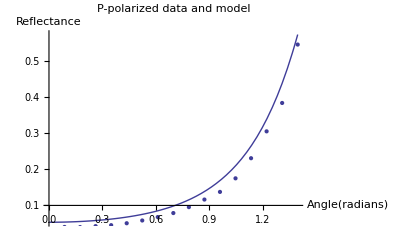

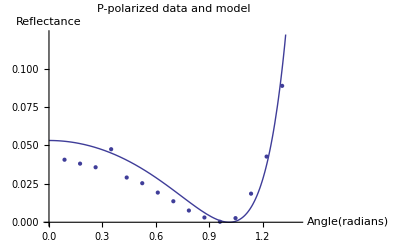

```mathematica
Show[Plot[Rs34,{θ1,0,80π/180}],ListPlot[plotDataS],PlotLabel->"P-polarized data and model",AxesLabel->{"Angle(radians)","Reflectance"}]
Show[Plot[Rp34,{θ1,0,80π/180}],ListPlot[plotDataP],PlotLabel->"P-polarized data and model",AxesLabel->{"Angle(radians)","Reflectance"}]
```

## 7 - Due 1-31-12

### P 3.12

```mathematica
λvac = 500; θ1 = π/4; n = 1.5;
```

```mathematica
z = λvac/(2π √((1.5/1)^2 Sin[π/4]^2-1))
```

225.079

### P 3.14

```mathematica
index = 0.13+4I;rp = (√(index^2-Sin[θ]^2)-index^2*Cos[θ])/(√(index^2-Sin[θ]^2)+index^2*Cos[θ]); Rp = Abs[rp]^2;
```

```mathematica
angle = θ/.FindRoot[Rp,{θ,π/4}]
```

1.31265

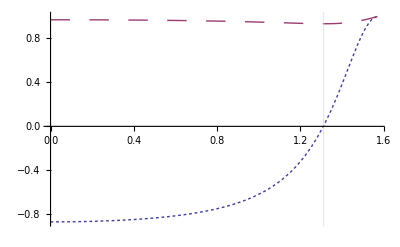

```mathematica
Plot[{Re[rp],Rp},{θ,0,π/2},GridLines->{{angle},{}},PlotStyle->{Dashing[Tiny],Dashing[Large]},PlotLegend->{"rs","Rp"}]
```

As shown in the plot Brewster's angle is at 1.31 rad, or about 75°

### P3.15

```mathematica
θ15 = 80*π/180; N15 = 0.13+4I;
```

```mathematica
rsMetal = (Cos[θ]-√(index^2-Sin[θ]^2))/(Cos[θ]+√(index^2-Sin[θ]^2));
rpMetal = (√(index^2-Sin[θ]^2)-index^2 Cos[θ])/(√(index^2-Sin[θ]^2)+index^2 Cos[θ]);
```

#### rs

```mathematica
rsMetal/.{θ->θ15,index->N15}//InputForm
```

-0.9938947662575262 - 0.08386448437208419*I

```mathematica
ArcTan[0.08386448437208419/0.9938947662575262]+π
√((.08386448437208419)^2+(.9938947662575262)^2)
```

3.22577

0.997427

#### rp

```mathematica
rpMetal/.{θ->θ15,index->N15}//InputForm
```

0.3626036409391114 - 0.8982206056475195*I

```mathematica
ArcTan[-0.8982206056475195/0.3626036409391114]
√((-0.8982206056475195)^2+0.3626036409391114^2)
```

-1.18711

0.968649

### P 4.2

```mathematica
ArcSin[1/2 Sin[0]]
```

0

```mathematica
α[θ2_,θ1_]:= Cos[θ2]/Cos[θ1]
β[n2_,n1_]:=n2/n1
ts[α_,β_]:=2/(1+α *β)
tp[α_,β_]:= 2/(α+β)
rs[α_,β_]:= (1-α β)/(1+α β)
rp[α_,β_]:= (α-β)/(α+β)
```

```mathematica
t[x_] =(ts[1,2]Exp[4π*I*Cos[0]/x*1*^-6]*ts[1,1.5/2])/(1-rs[1,2]*rs[1,1.5/2]*Exp[4π*I*Cos[0]/x*1*^-6]);
```

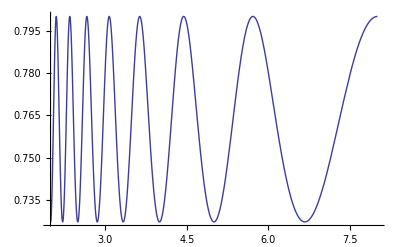

```mathematica
Plot[Abs[t[x]],{x,200*^-9,800*^-9}]
```

### 4.4

#### Part a algebra for finding F

```mathematica
(4((n-1)/(n+1))^2)/((1-((n-1)/(n+1))^2)^2)//FullSimplify
```

((n^2-1)^2)/(4 n^2)

#### Part b min calculation

```mathematica
1/(1+((1.5^2-1)^2)/(4 (1.5)^2))
```

0.852071

#### part c: λ for max efficiency

```mathematica
2*1.5*150*^3
```

450000.

## 8 - Due 2-2-12

### 4.6

```mathematica
θ0 = θ2 = π/4; θ1 = ArcSin[1.5  Sin[θ0]]; n1 = 1; n0=n2 = 1.5;
α01 = Cos[θ1]/Cos[θ0];
α12 = Cos[θ2]/Cos[θ1];
β01 = n1/n0;
β12 = n2/n1;
k1 = 2.22I  (d/λ);
```

```mathematica
Ts [d_]=(Abs[ts[α01,β01]]^2* Abs[ts[α12,β12]]^2)/Abs[1 - Exp[4.996183089593019+2I*k1]]^2
```

1.44/(Abs[1-ⅇ^(4.99618-((4.44+0. ⅈ) d)/λ)]^2)

### L 4.7

```mathematica
T[d_] = 1.44/Abs[Exp[-I*k1] - Exp[4.996I]*Exp[I*k1]]^2;
```

```mathematica
data = ({{0.2, 32}, {1/2, 28.1}, {1, 16.5}, {3/2, 11}, {2, 6.2}, {5/2, 2.2}, {3, 1.9}, {7/2, 0.04}, {4, 0.002}});
```

```mathematica
adjustedData  =Transpose[data][[2]]/32
```

{1,0.878125,0.515625,11/32,0.19375,0.06875,0.059375,0.00125,0.0000625}

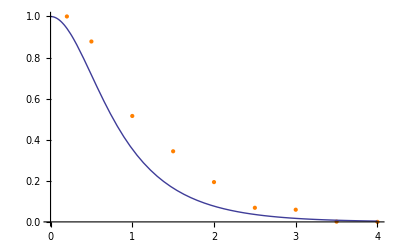

```mathematica
Show[{ListPlot[Transpose[{Transpose[data][[1]],adjustedData}],PlotStyle->{Thick,Orange}]},Plot[T[d],{d,0,4}]]
```

### 4.8

```mathematica
R = 0.9; t = 0.05; a = 0.05; d = 0.5*^7; n = 1; λ = 587;θ =0;F =(4R)/(1-R)^2 ;
```

```mathematica
Tmax = t^2/(1-R)^2
```

0.25

```mathematica
Tmin = Tmax/(1+F)
```

0.000692521

```mathematica
λfsr = λ^2/(2*n d Cos[θ])
```

0.0344569

```mathematica
λfwhm = λ^2/(π n d Cos[θ] √F)
```

0.00115613

```mathematica
Rp = λ/λfwhm
```

507730.

### 4.9

```mathematica
TMax = 1; F = 10; λ = 500; d1 = 1*^7; n =1; d2 =1.00001*^7;
```

```mathematica
t[θ_] = TMax/(1+F*Sin[(4 π n d)/λ Cos[θ]]^2)
```

1/(10 sin^2(1/125 π d cos(θ))+1)

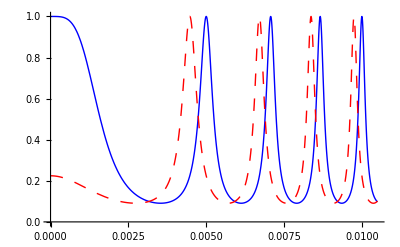

```mathematica
Plot[{t[θ]/.d->d1,t[θ]/.d->d2},{θ,0,10.5*^-3},PlotLegend->{"d = 1cm","d = 1.00001 cm"},PlotStyle->{{Blue,Dashing[Thick]},{Red,Dashing[Medium]}},LegendShadow->{-0.05,-0.05}, LegendSize->0.78]
```

## 9 - Due 2-7-12

### 4.10

```mathematica
√((633*^-9)/(0.5*^-2))
```

0.0112517

### 4.13

```mathematica
({{1, -1}, {n1 Cos[θ1], n1 Cos[θ1]}}).Inverse[({{Exp[I β1], -Exp[-I β1]}, {n1 Cos[θ1]Exp[I β1], n1 Cos[θ1]Exp[-I β1]}})]//FullSimplify
```

(cos(β1) | -(ⅈ sec(θ1) sin(β1))/n1
-ⅈ n1 cos(θ1) sin(β1) | cos(β1))

### 4.17

#### Part a

```mathematica
β = π /2;
```

```mathematica
A = 1/2*({{1, 1}, {1, -1}}).({{Cos[β], -I Sin[β]/n1}, {-I n1 Sin[β], Cos[β]}}).({{1, 0}, {ng, 0}})
```

(1/2 (-ⅈ n1-(ⅈ ng)/n1) | 0
1/2 (ⅈ n1-(ⅈ ng)/n1) | 0)

#### Part b

```mathematica
Ab =  1/2*({{1, 1}, {1, -1}}).({{Cos[β], -I Sin[β]/n1}, {-I n1 Sin[β], Cos[β]}}).({{Cos[β], -I Sin[β]/n2}, {-I n2 Sin[β], Cos[β]}}).({{1, 0}, {ng, 0}})
```

(1/2 (-n2/n1-(n1 ng)/n2) | 0
1/2 ((n1 ng)/n2-n2/n1) | 0)

#### Part c

```mathematica
na = 2.32; nb = 1.63; nc = 1.38;
```

```mathematica
trials = {{na,nb},{na,nc},{nb,na},{nb,nc},{nc,na},{nc,nb}};
```

```mathematica
R[{n1_,n2_}] := ((n2^2 - 1.5 n1^2)/(n2^2+1.5 n1^2))^2
```

```mathematica
ans = Table[R[x]/.x->  trials[[i]],{i,1,6}]
```

{0.254818,0.38227,0.0222409,0.124833,0.0939829,0.0013119}

```mathematica
ans[[6]]==Min[ans]
```

True

### 4.18

```mathematica
n1 = 1.6; n2 = 2.1; ng = 1.5; θ1 = θ2 = θ0 = 0; λvac = 550;l[n_] :=λvac/(4 n) 
l1 = l[n1];
l2 = l[n2];
```

```mathematica
β18[λ_,n_]:= (2 π n)/λ*l[n]
```

```mathematica
M[λ_,n_]:= ({{Cos[β18[λ,n]], -I Sin[β18[λ,n]]/n}, {-I n Sin[β18[λ,n]], Cos[β18[λ,n]]}})
```

```mathematica
A[λ_,layers_]:= 1/2({{1, 1}, {1, -1}}).MatrixPower[M[λ,n1].M[λ,n2],layers].({{1, 0}, {1.5, 0}})
```

```mathematica
r[λ_,layers_]:= (A[λ,layers][[2,1]])/(A[λ,layers][[1,1]])
```

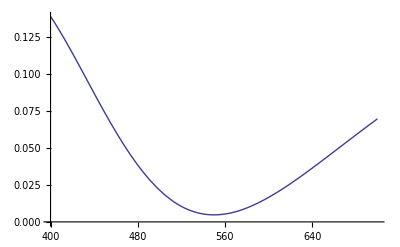

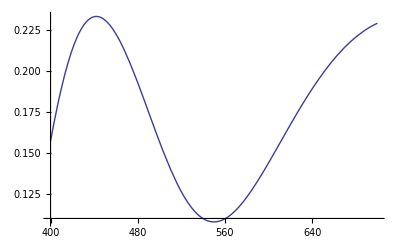

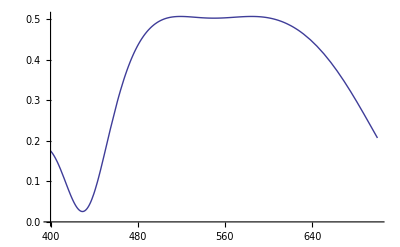

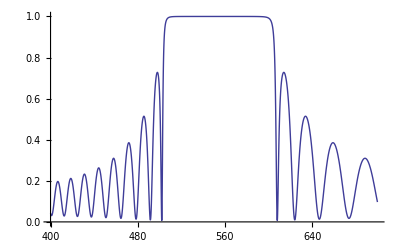

```mathematica
Plot[Abs[r[λ,1]]^2,{λ,400,700}]
Plot[Abs[r[λ,2]]^2,{λ,400,700}]
Plot[Abs[r[λ,4]]^2,{λ,400,700}]
Plot[Abs[r[λ,25]]^2,{λ,400,700}]
```

## 10 - Due 2-9-12

### 5.2

```mathematica
fresnel[{nx_,ny_,nz_},{ux_,uy_,uz_}]:=Module[{},
Solve[1/n^2==ux^2/(n^2-nx^2)+ uy^2/(n^2-ny^2)+uz^2/(n^2-nz^2),n]

]
```

```mathematica
fresnel[{1.5,1.6,2.0},{1/√14,2/√14,3/√14}]
```

{{n→-1.70499},{n→-1.51272},{n→1.51272},{n→1.70499}}

### 5.6

```mathematica
λvac = 633; no= 1.54424; ne = 1.55335;d = 0.96*^6;
np[θi_]:=(no ne)/(√(no^2 Sin[θi]^2+ne^2 Cos[θi]^2))
δ [θi_]:= d(Tan[θs[θi]]-Tan[θp[θi]])Sin[θi]
 θs[θi_]:=ArcSin[Sin[θi]/no]
θp[θi_]:= ArcTan[(ne Sin[θi])/(no √(ne^2-Sin[θi]^2))]
λs[θi_]:=d/((λvac/no)Cos[θs[θi]])
λp[θi_]:= d/((λvac/np[θi])Cos[θp[θi]])+δ[θi]/λvac
```

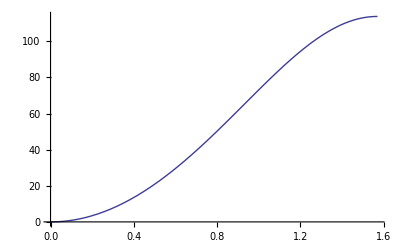

```mathematica
Plot[2π * (-λs[x]+λp[x]),{x,0,π/2}]
```

### L 5.7

```mathematica
bright = {20,30,39,48,56,63}*π/180;
dim = {24,35,43,51,59}*π/180;
```

```mathematica
newBrightData =Transpose[{bright, Table[2π*(λp[bright[[i]]]-λs[bright[[i]]]),{i,1,6}]}];
newDimData =Transpose[{dim, Table[2 π *(λp[dim[[i]]]-λs[dim[[i]]]),{i,1,5}]}];
```

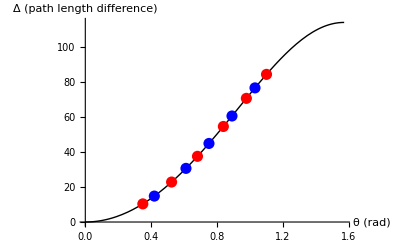

```mathematica
Show[Plot[2π * (-λs[x]+λp[x]),{x,0,π/2},PlotStyle->Black,AxesLabel->{"θ (rad)","Δ (path length difference)"}],ListPlot[newBrightData,PlotStyle->{Red,PointSize[.02]}],ListPlot[newDimData,PlotStyle->{Blue,PointSize[.02]}]]
```

## Review Session

### R20

#### (a) By inspection of the figure, write down similar expressions for the reflected and transmitted fields (i.e. E_r and E_t).

E_r = [E_r^(p)(ŷ cos θ_r + ẑ sin θ_r) + x̂ E_r^(s)]e^(ι (k_r(y sin θ_r- z cos θ_r) - ω_r t))

E_t = [E_t^(p)(ŷ cos θ_t - ẑ sin θ_t) + x̂ E_t^(s)]e^(ι (k_t(y sin θ_t+ z cos θ_t) - ω_t t))

#### (b) Find an expression relating E_i, E_r, and E_t using the boundary condition at the interface. From this expression obtain the law of reflection and Snell’s law.

At the interface, z =0.

(E_L)_(||) = (E_R)_(||)

E_i+E_r=E_t

(E_i^(p)ŷ cos θ_i  + x̂ E_i^(s))e^(ι (k_i y sin θ_i - ω_i t))+ (E_r^(p)ŷ cos θ_r  + x̂ E_r^(s))e^(ι (k_r y sin θ_r - ω_r t)) = (E_t^(p)ŷ cos θ_t  + x̂ E_t^(s))e^(ι (k_t y sin θ_t - ω_t t))

This must hold for all y,t which leads to  ω_i = ω_r = ω_t = ω and k_i sin θ_i = k_r sin θ_r = k_t sin θ_t

Because k_r=k_i we know that θ_r must be equal to θ_i, this is the law of reflection. 

Also, because there no absorbtion k = nω/c and we can get snell’s law: n_i sinθ_i = n_t sin θ_t

#### (c) The boundary condition requiring that the tangential component of B must be continuous leads to

n_i(E_i^(p) - E_r^(p)) = n_t E_t^(p)
n_i(E_1^(s) - E_r^(s)) cos θ_i = n_t E_t^(s)cos θ_t

Use this and the results from part (b) to derive

r_p≡E_r^(p)/E_i^(p) = -(tan(θ_1-θ_t))/(tan(θ_i+θ_t))

Starting with the boundary condition result from part b and the one given above, solving only for the p-polarized light, and using the conditions explained above we obtain these two equations:

E_i cos θ_i ŷ + E_r cos θ_r ŷ = E_t cos θ_t ŷ

n_i(E_i^(p) - E_r^(p)) = n_t E_t^(p)

E_i cos θ_i ŷ + E_r cos θ_r ŷ = E_t cos θ_t ŷ |   | n_i(E_i^(p) - E_r^(p)) = n_t E_t^(p)
E_i+E_r = (cos θ_t)/(cos θ_i)E_t |   | E_i-E_r = n_2/n_1 E_t=(sin θ_i)/(sin θ_t)E_t
  | 2 E_i=((cos θ_t)/(cos θ_i)+(sin θ_i)/(sin θ_t))E_t  |  
  | 2 E_r = ((cos θ_t)/(cos θ_i)-(sin θ_i)/(sin θ_t))E_t |  
  | E_r/E_i = (cos θ_t sin θ_t - cos θ_i sin θ_i)/(cos θ_t sin θ_t + cos θ_i sin θ_i) = -(tan (θ_i-θ_t))/(tan (θ_i+θ_t)) |

## 13 - Due 2-23-12

### P6.6

### L6.9

```mathematica
quarter[θ_]:=({{Cos[θ]^2+ I Sin[θ]^2, Sin[θ]Cos[θ] - I Sin[θ]Cos[θ]}, {Sin[θ]Cos[θ] - I Sin[θ]Cos[θ], Sin[θ]^2+I Cos[θ]^2}})
linearJones[θ_]:=({{Cos[θ]}, {Sin[θ]}})
```

```mathematica
inverse = Conjugate[quarter[50Degree]]//N;
```

```mathematica
elip = inverse.linearJones[(73+90)Degree]
```

(-0.251157+0.705148 ⅈ
-0.299317-0.591689 ⅈ)

```mathematica
A =Norm[elip[[1]]]
Arg[elip[[1]]][[1]]
```

0.748541

1.91296

```mathematica
B = Norm[elip[[2]]]
Arg[elip[[2]]][[1]]
```

0.663089

-2.03913

```mathematica
δ = (Arg[elip[[2]]][[1]] - Arg[elip[[1]]][[1]])+ 2π
```

2.33109

```mathematica
α = 1/2 ArcTan[(2 A B Cos[δ])/(A^2-B^2)]
```

-0.698132

```mathematica
Eα = √(A^2 Cos[α]^2 + B^2 Sin[α]^2+ A B Cos[δ] Sin[2α])
```

0.920505

```mathematica
Eα2 = √(A^2 Sin[α]^2 + B^2 Cos[α]^2- A B Cos[δ] Sin[2α])
```

0.390731

```mathematica
Eα2/Eα
```

0.424475

```mathematica
α*180/π
```

-40.

### P6.11

```mathematica
({{-0.96865 Exp[-I*1.1871], 0}, {0, 0.99743*Exp[I*3.0574]}}).({{1/√2}, {1/√2}})
```

(-0.256407+0.635135 ⅈ
-0.702791+0.0593101 ⅈ)

```mathematica
1.1871+3.0574
```

4.2445

```mathematica
-0.96865/√2
```

-0.684939

```mathematica
0.99743/√2
```

0.70529

### P0.24

```mathematica
ft[t_]:= E0*Exp[-(t/T)^2]*Cos[ω0 *t]
```

```mathematica
fω=Assuming[T>0,1/(√(2π))Integrate[ft[t]*Exp[I ω t],{t,-∞,∞}]]
```

(E0 T ⅇ^(-1/4 T^2 (ω+ω0)^2) (ⅇ^(T^2 ω ω0)+1))/(2 √2)

### P0.25

```mathematica
inverseTransform = Assuming[T>0, 1/(√(2π))Integrate[fω*Exp[-I ω t],{ω,-∞,∞}]]
```

1/2 E0 (1+ⅇ^(2 ⅈ t ω0)) ⅇ^(-t (t/T^2+ⅈ ω0))

```mathematica
ft[t] - inverseTransform//FullSimplify
```

0

## 14 - Due 2-28-12

### 0.28d

```mathematica
f[t_] := Exp[-t^2/(2T^2)]*Sin[ω0 t]
F[ω_] :=Assuming[T∈ Reals && T>0, FourierTransform[f[t],t,ω]]
```

```mathematica
F[ω]//TrigToExp (* This just verified that I got the same answer for part c*)
```

1/2 ⅈ T ⅇ^(-1/2 T^2 (ω-ω0)^2)-1/2 ⅈ T ⅇ^(-1/2 T^2 (ω+ω0)^2)

```mathematica
plotFourierTransform = Im[F[ω]]//TrigToExp
```

-1/4 Re(T (ⅇ^(1/2 T^2 (ω-ω0)^2)-ⅇ^(-1/2 T^2 (ω-ω0)^2)))+1/4 Re(T (ⅇ^(-1/2 T^2 (ω-ω0)^2)+ⅇ^(1/2 T^2 (ω-ω0)^2)))+1/4 Re(T (ⅇ^(1/2 T^2 (ω+ω0)^2)-ⅇ^(-1/2 T^2 (ω+ω0)^2)))-1/4 Re(T (ⅇ^(-1/2 T^2 (ω+ω0)^2)+ⅇ^(1/2 T^2 (ω+ω0)^2)))

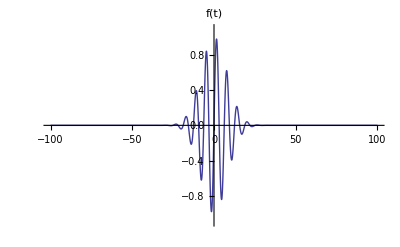

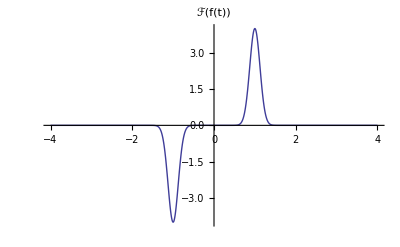

```mathematica
Plot[f[t]/.{T->8,ω0->1},{t,-100,100},PlotLabel->"f(t)",PlotRange->{-1.1,1.1}]
Plot[plotFourierTransform/.{T->8,ω0->1},{ω,-4,4},PlotLabel->"ℱ(f(t))",PlotRange->All]
```

### Colton 4

```mathematica
H[ω_]:=(-I*T)/2(Exp[-(ω+ω0)^2 T^2/2] - Exp[-(ω-ω0)^2 T^2/2])*(2 Cos[ω *t0] +1)
```

```mathematica
fourierHPlot = Im[H[ω]]/.{T->8,ω0->1, t0->30}
```

-4 Re((ⅇ^(-32 (ω+1)^2)-ⅇ^(-32 (ω-1)^2)) (2 cos(30 ω)+1))

```mathematica
h[t_]:= Sum[Exp[-i^2/(2 T^2)]Sin[ω0 i],{i,{t-t0,t,t+t0}}]
```

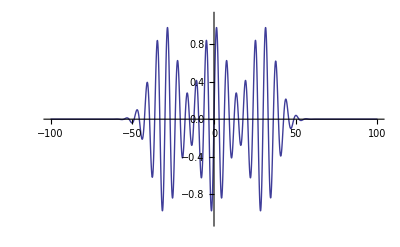

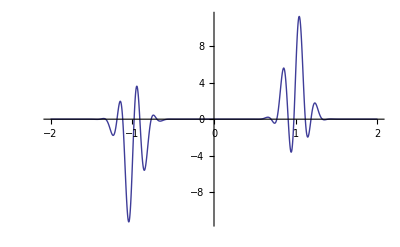

```mathematica
Plot[h[t]/.{T->8,ω0->1, t0->30},{t,-100,100},PlotRange->{-1.1,1.1}]
Plot[fourierHPlot,{ω,-2,2},PlotRange->All]
```

### P7.5

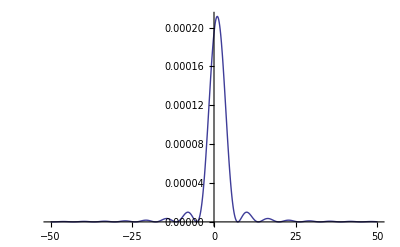

```mathematica
Plot[3*^8*8.8542*^-12*1/(4 π)Sinc[1/2(w-1)]^2,{w,-50,50},PlotRange->All]
(* In the plot below I let T = Subscript[E, 0] = n = Subscript[ω, 0] = 1 *)
```

## 15 - Due 3-1-12

### P7.7

```mathematica
c = 3*^8; λ0 = 800*^-9; z = 0.01; ω0 = (2 π c)/λ0; T = (25*^-15)/(2 √Log[2]);ϵ0 = 8.8542*^-12;
```

```mathematica
n = 1.4948 + 0.016;n1 = 0.016/ω0;k0 =ω0*n/c;vin = n/c  + ω0 n1/c;α =n1/c+0;Φ = (2 α)/T^2 z;τ = T √(1+Φ^2);
```

```mathematica
Eafter = E0/(√(τ/T))*Exp[(-(t - z*vin)^2)/(2 τ^2)]*Exp[-I*(t - z*vin)^2/(2 τ^2)*Φ + I(k0*z-ω0*t) + I*1/2 ArcTan[Φ]];
```

```mathematica
Eafter//Chop
```

0.667636 E0 exp(ⅈ (118658.-750000000000000 π t)+(0.+0.554399 ⅈ)+(-4.40691×10^26-8.85028×10^26 ⅈ) t^2)

```mathematica
Iafter = ComplexExpand[(n ϵ0 c)/2*Eafter*Conjugate[Eafter]]//Chop
```

0.00089439 E0^2 ⅇ^(-8.81382×10^26 t^2)

```mathematica
ans = t/.Solve[ⅇ^(-8.813820930320749*^26 t^2)==1/2,t][[2]]
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

2.80434×10^-14

```mathematica
ans*2
```

5.60868×10^-14

## 16 - Due 3-6-12

### P8.4

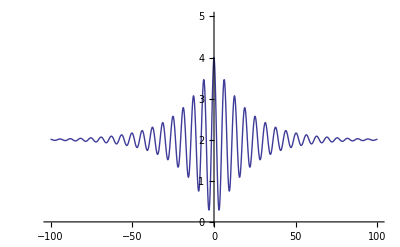

```mathematica
Plot[2*(1+Exp[-Abs[τ *0.1/2]]*Cos[τ]),{τ,-100,100},PlotRange->{0,5}]
```

### P8.7

```mathematica
2.0/(1.0*^-3)*500*^-9
```

0.001

```mathematica
1/((500*^-9/1.5)/(0.01*^-3))
1/0.05-1/((500*^-9/1.5)/(0.01*^-3))
```

30.

-10.

## Review 2

### R42

#### a.)

General Equation for linear polarizer: (Cos^2 θ | Sinθ Cosθ
Sin θ | Sin^2 θ)
General Equation for Jones Vector: (A
B e^ιδ)
Horizontal Polarizer: θ = 0° -> M_h = (1 | 0
0 | 0)
Vertical PolarizerL θ =  90°→ M_v = (0 | 0
0 | 1)
Horizonatally Polarized Starting light: (1
0)

Remember that you do the multiplication “Backwards”

```mathematica
({{0, 0}, {0, 1}}).({{1, 0}, {0, 0}}).({{1}, {0}})//MatrixForm
```

(0
0)

#### b.)

Linear polarizer: θ =45°: (Cos^2 45 | Sin45 Cos45
Sin 45 | Sin^2 45)  = (1/2 | 1/2
1/2 | 1/2)

```mathematica
({{0, 0}, {0, 1}}).({{1/2, 1/2}, {1/2, 1/2}}).({{1, 0}, {0, 0}}).({{1}, {0}})//MatrixForm
```

(0
1/2)

I = 1/2 n c ϵ_0 E·E^* =1/2 n c ϵ_0 (0 | 1/2)  (0
1/2) =1/2 n c ϵ_0 1/4

#### c.)

General Equation for λ/4 waveplate: (Cos^2 θ + ⅈ Sin^2 θ | Sinθ Cosθ - ⅈ Sinθ Cosθ
Sinθ Cosθ - ⅈ Sinθ  Cosθ | Sin^2 θ + ⅈ Cos^2 θ)
λ/4 waveplate: θ = 45°→(Cos^2 45 + ⅈ Sin^2 45 | Sin45 Cos45 - ⅈ  Sin45 Cos45
Sin45 Cos45 - ⅈ Sin45 Cos45 | Sin^2 45 + ⅈ Cos^2 45)=  (1/2+ ⅈ 1/2 | 1/2- ⅈ 1/2
1/2 - ⅈ 1/2 | 1/2+ ⅈ 1/2)

```mathematica
({{0, 0}, {0, 1}}).({{1/2+ I 1/2, 1/2- I 1/2}, {1/2 - I 1/2, 1/2+ I 1/2}}).({{1, 0}, {0, 0}}).({{1}, {0}})//MatrixForm
```

(0
1/2-ⅈ/2)

I = 1/2 n c ϵ_0 E'·E^* =1/2 n c ϵ_0 (0 | 1/2-ⅈ/2)  (0
1/2+ⅈ/2) =1/2 n c ϵ_0 1/2

### R43

#### (a) Find the Jones matrix for half wave plate with its fast axis making an arbitrary angle θ with the x-axis. HINT: Project an arbitrary polarization with Ex and Ey onto the fast and slow axes of the wave plate. Shift the slow axis phase by π, and then project the field components back onto the horizontal and vertical axes.

### R44

#### a.) What is the spectral content (i.e., I (ω)) of a square laser pulse: E(t) = Piecewise[{{E_0 e^(-i ω_0 t), |t| ≤τ/2}, {0, |t|≥ τ/2}}] Make a sketh of I(ω), indicating the location of the first zeroes

#### b.) What is the temporal shape (i.e., I (t )) of a light pulse with frequency content E(ω) = Piecewise[{{E_0, |ω- ω_0| ≤ Δω/2}, {0, |ω- ω_0| ≥ Δω/2}}] where in this case E_0 has units of E-field per frequence. Make a sketch of I(t), indicating the location of the first zeroes

#### c.) If E (ω) is known (any arbitrary function, not the same as above), and the light goes through a material of thickness l and index of refraction n (ω), how would you find the form of the pulse E (t ) after passing through the material? Please set up the integral.

### R45

#### a.) Prove Parseval’s theorem: ∫_(-∞)^∞ |E(ω)|^2 ⅆω = ∫_(-∞)^∞ |E(t)|^2 ⅆt Hint: δ(t’-t) = 1/(2π)∫_(-∞)^∞ e^(ⅈ ω (t'-t))ⅆω

#### b.) (b) Explain the physical relevance of Parseval’s theorem to light pulses. Suppose that you have a detector that measures the total energy in a pulse of light, say 1 mJ directed onto an area of 1 mm2. Next you measure the spectrum of light and find it to have a width of Δλ = 50 nm, centered at λ_0 = 800 nm. Assume that the light has a Gaussian frequency profile: I(ω) = I(ω_0)(e^-((ω- ω_0)/δω))^2 Use as an approximate value δω ∼= 2πc \[Laplace]λ. Find a value and correct units for I (ω0). HINT: ∫_(-∞)^∞ e^(-Ax^2 + Bx +c)ⅆx = √(π/A)e^(B^2/4A+c)

### R46

Continuous light entering a Michelson interferometer has a spectrum described b:

I(ω) = Piecewise[{{I_0, |ω- ω_0| ≤ Δω/2}, {0, |ω- ω_0| > Δω/2}}]
The Michelson interferometer uses a 50:50 beam splitter. The emerging light has intensity ⟨I_det(t,τ)⟩_t = 2⟨I(t)⟩_t[1+ Re{γ(τ)}], where degree of coherence is:

γ(τ) = (∫_(-∞)^∞ I(ω)e^(-ⅈω τ)ⅆω)/(∫_(-∞)^∞ I(ω)ⅆω)
Find the frindge Visibility V = (I_max-I_min)/(I_max+ I_min) as a function of.

### R47

Light emerging from a point travels by means of two very narrow slits to a point y on a screen. The intensity at the screen arising from a point source at position y′ is found to be

I_screem(y',h) = 2I(y'){1+cos[k h (y/D+y'/r)]}

where an approximation has restricted us to small angles

#### a.) Now, suppose that I(y′) characterizes emission from a wider source with randomly varying phase across its width. Write down an expres- sion (in integral form) for the resulting intensity at the screen: I_screen(h) = ∫_(-∞)^∞ I_screem(y',h)ⅆy'

#### b.) Assume that the source has an emission distribution with the form I(y’) = (I_0/Δy')E^(-(y')^2/(Δy')^2). What is the function γ(h) where the intensity is written I_screen(h) = 2 √π I_0[t+Re{γ(h)}]? Hint: ∫_(-∞)^∞ e^(-Ax^2 + Bx +c)ⅆx = √(π/A)e^(B^2/4A+c)

#### c.) As h varies, the intensity at a point on the screen y oscillates. As h grows wider, the amplitude of oscillations decreases. How wide must the slit separation h become (in terms of R, k, and \[Laplace]y′) to reduce the visibility to V = (I_max-I_min)/(I_max + I_min) = 1/3

## 19 - Due 3-20-12

### 9.11

```mathematica
general = p*a+b+p*q*c+q*d==0;
eq1 =l*a + b + 2 l^2*c + 2 l * d==0;
eq2 = 2l*a + b + 3 l^2*c + 3/2 l * d==0;
eq3 = -1/2==a+3*l/2*c;
eq4 = a*d-b*c==1;
```

```mathematica
{a11,b11,c11,d11}={a,b,c,d} /.Solve[{eq1&&eq2&&eq3&&eq4},{a,b,c,d}][[1]];
({{a11, b11}, {c11, d11}})//MatrixForm
```

(1 | l
-1/l | 0)

### 9.12

```mathematica
{{a12,b12},{c12,d12}} = ({{1+5/5(1/1.5-1), 5*1/1.5}, {-(1.5-1)(1/5-1/(-10))+5/(5*(-10))(2-1/1.5-1.5), 1-5/-10(1/1.5-1)}})
p1 = (1-d12)/c12
p2 = (1-a12)/c12
f = -1/c12
```

(0.666667 | 3.33333
-0.133333 | 0.833333)

-1.25

-2.5

7.5

### 9.13

```mathematica
ps = {.188,.2175,.271};
qs = {3.705,1.7925, .955};
eq = {Null,Null,Null};
```

```mathematica
Table[ eq[[i]]= general/.{p->ps[[i]],q->qs[[i]]},{i,1,3}];
```

```mathematica
{a13,b13,c13,d13} = {a,b,c,d}/.Quiet[Solve[eq[[1]]&&eq[[2]]&&eq[[3]]&&a*d-b*c==1,{a,b,c,d}][[2]]];
({{a13, b13}, {c13, d13}})//MatrixForm
p131 = (1-d13)/c13;
p132 = (1-a13)/c13;
f = -1/c13;
Print["f= ",f,"  p1=",p131,"  p2= ",p132]
```

(0.257184 | 0.26794
-3.23106 | 0.522071)

f= 0.309496  p1=-0.147917  p2= -0.229898

### 9.14

```mathematica
thickLensMatrix[d_,r1_,r2_,n_]:= ({{1+d/r1(1/n-1), d/n}, {(1-n)(1/r1-1/r2) + d/(r1*r2)(2-1/n-n), 1-d/r2(1/n-1)}})
```

```mathematica
m1 = thickLensMatrix[0.357,1.628,-27.57,1.6116];
m2 = ({{1, 0.189}, {0, 1}});
m3 = thickLensMatrix[0.081,-3.457,1.582,1.6053];
m4 = ({{1, 0.325}, {0, 1}});
m5= thickLensMatrix[0.217,-∞,1.920,1.5123];
m6 = thickLensMatrix[0.396,1.920,-2.400,1.6116];
m6.m5.m4.m3.m2.m1//MatrixForm
```

(0.867538 | 1.33868
-0.196895 | 0.848862)

## 20 - Due 3-22-12

### P9.15

#### a.)

```mathematica
emptySpaceMatrix[d_]:=({{1, d}, {0, 1}})
mirrorMatrix [R_]:=({{1, 0}, {-2/R, 1}})
```

```mathematica
m1 = m3  = emptySpaceMatrix[L]; m2 = mirrorMatrix[R1]; m4 = mirrorMatrix[R2];
abcd15 = ({{a15, b15}, {c15, d15}})=m1.m2.m3.m4;abcd15//FullSimplify
```

((4 L^2-2 (2 R1+R2) L+R1 R2)/(R1 R2) | L (2-(2 L)/R1)
-(2 (-2 L+R1+R2))/(R1 R2) | 1-(2 L)/R1)

Now we see equation 9.70 in the book and know that cos[θ] = 1/2(A+D) from the matrix I defined as abcd15 above. The only condition on that equation is that we have a real angle so that means that |1/2(A+D)|≤ 1 or -1 < 1/2(A+D) <1.
We are asked to prove that is the same as 0< (1-L/R1) (1-L/R2) <1.
To get to that point we will have to make the bounds of the first inequality the same as the one in the previous line by adding one to both sides and dividing by two. The result is 0 < (1/2(A+D)+1)/2 <1. 
We will be done with the proof if we show that (1/2(A+D)+1)/2 = (1-L/R1) (1-L/R2). This is shown below.

```mathematica
(1/2(a15+d15)+1)/2- (1-L/R2)*(1-L/R1)//FullSimplify
```

0

#### b.)

Let R1 = 60cm and R2 = 100 cm.  We will now plug that in and find appropriate values for L.

```mathematica
ans15b = Reduce[0<((1-L/R2)*(1-L/R1)/.{R1->60,R2->100})<1,L];
Print["The first range is:   ", ans15b[[1]],"     and the second range is:   ",ans15b[[2]]]
```

The first range is:   0<L<60     and the second range is:   100<L<160

### L9.17

Let R1 = ∞, R2 = 80cm. Below is an expected theoretical range for the acceptable values of L

```mathematica
Reduce[0<((1-L/R2)*(1-L/R1)/.{R1->80,R2->∞})<1,L]
```

0<L<80

We measured a max value of L to be 61.5 cm. This is different than the theoretical max of 80cm. 
It is possible that the numbers are different because of human (our) error in measuring the distance and finding the orentation for the mirror so we could get it to lase.
Another potential reason for error is that the 80cm raduis of curvature might not be exact.

### P10.1

```mathematica
ArcSin[1/2*Sin[45.5Degree]]*180/π
```

20.8931

### P 10.2

### a.) On sheet

### b.)

Using these equations for divergence and curl in spherical coordinates (the top one is the divergence and the bottom one is the curl):
-Graphics-

```mathematica
e[r_,t_]:=A/r Cos[k r - ω t]
```

#### i.) ∇·E = ρ/ϵ_0. In this case our E is only in the ϕ direction so E_r, E_θ are both zero as well as their derivatives. Also, E_ϕ has no ϕ dependence so(∂E_ϕ)/(∂ϕ)=0 and ∇·E =0. Gauss Law is violated.

#### ii.) ∇×E = (-∂B)/(∂t)

The only terms that survive the curl equation are the first on in the r̂ direction and the second one in the θ̂ direction.

```mathematica
Print["∇×E = ",b1=1/r*-D[e[r,t]*r,r],"θ̂","  +  ",b2 =1/(r Sin[θ])*D[e[r,t]*Sin[θ],θ]//Simplify,"r̂"]
```

∇×E = (A k sin(k r-t ω))/r θ̂  +  (A cos(k r-t ω) cot(θ))/r^2 r̂

Faraday’s law says that ∇×E = (∂B)/(∂t). To solve for B you need to integrate both sides with respect to t. This is shown below.

```mathematica
Print["B = ",bθ = Integrate[b1,t]//Simplify,"θ̂   ", br =Integrate[b2,t]//Simplify,"r̂"]
```

B = (A k cos(k r-t ω))/(r ω)θ̂   -(A cot(θ) sin(k r-t ω))/(r^2 ω)r̂

#### iii.) Using this for B, show that Gauss’s Law for magnetism is violated (∇·B = 0)

Using the first eqution (for the divergence of a vector field in spherical coordinates, we computer ∇·B below)

```mathematica
Print["∇·B = ",1/r^2*D[r^2*br,r] + 1/(r * Sin[θ])*D[bθ*Sin[θ],θ]," ∴ Gauss's Law for magnetism holds"]
```

∇·B = 0 ∴ Gauss's Law for magnetism holds

#### iii.) Ampre’s Law states ∇×B = ϵ_0(∂E)/(∂t) +J. Using the second equation with our expression for B we see get the following for the curl of B:

```mathematica
Print["∇×B = ",1/(r Sin[θ])*(-D[bθ,ϕ])//Simplify," r̂  +", 1/r(1/Sin[θ] D[br ,ϕ] - D[r*0,r])//Simplify, "  θ̂  + ", 1/r(D[r*bθ,r] - D[br,θ])//Simplify,"ϕ̂ "]
Print["(∂E)/(∂t) = ",D[e[r,t],t]//Simplify, "ϕ̂ "]
Print["As can be seen below these two statements, plus some constants, are not equal ∴ Ampre's Law is violated"]
```

∇×B = 0 r̂  +0  θ̂  + -(A (k^2 r^2+csc^2(θ)) sin(k r-t ω))/(r^3 ω)ϕ̂

(∂E)/(∂t) = (A ω sin(k r-t ω))/r ϕ̂

As can be seen below these two statements, plus some constants, are not equal ∴ Ampre's Law is violated

## 21 - Due 3-27-12

### 10.6

#### a.) Find diffraction pattern under Fresnel and Franhaufer approximations for on-axis cylindrical aperature.

Fresnel in Cylindrical Coordinates (eqn.1 10.27): E(ρ,x) = -(2 π ⅈϵ^(ⅈ k z)ⅇ^((ⅈ k ρ^2)/(2z)))/(λ z)∫ρ'ⅆρ'E[ρ',0]ⅇ^(ⅈ kρ'^2/(2z))J_0((k ρ ρ')/z)
     With ρ =0 this simplifies to E(ρ,x) = -(2 π ⅈϵ^(ⅈ k z))/(λ z)∫ρ'ⅆρ' E_0 ⅇ^(ⅈ kρ'^2/(2z)) because ⅇ^0=J_0(0) = 1 and E_0 = E[ρ',0]

We will then integrate from 0 to  ℓ/2 where ℓ is the diameter of our aperature.

```mathematica
Print["Fresnel Approx. reduces to E[0,z] = ", fresnel = (-2π I Exp[I k z]*E0)/(λ z)*Integrate[ρ* Exp[I*k*ρ^2/(2 z)],{ρ,0,ℓ/2}]//FullSimplify]
```

Fresnel Approx. reduces to E[0,z] = -(2 ⅇ^(ⅈ k z) (-1+ⅇ^((ⅈ k ℓ^2)/(8 z))) E0 π)/(k λ)

Fraunhoffer in cylindrical coordinates (eqn. 10.28): E(ρ,x) = -(2 π ⅈϵ^(ⅈ k z)ⅇ^((ⅈ k ρ^2)/(2z)))/(λ z)∫ρ'ⅆρ' E_0 J_0((k ρ ρ')/z)
     When ρ=0 this simplifies to E(ρ,x) = -(2 π ⅈϵ^(ⅈ k z))/(λ z)∫ρ'ⅆρ' E_0 ⅇ^0=J_0(0) = 1 and E_0 = E[ρ',0]
We now integrate from 0 to ℓ/2

```mathematica
Print["Fraunhoffer Approx. reduces to E[0,z] = ", fraun = (-2π I Exp[I k z]*E0)/(λ z)*Integrate[ρ,{ρ,0,ℓ/2}]//FullSimplify]
```

Fraunhoffer Approx. reduces to E[0,z] = -(ⅈ ⅇ^(ⅈ k z) E0 π ℓ^2)/(4 z λ)

Equation 10.3 is below:

```mathematica
Print["Equation 10.3 is I(0,z):    ", eq103 = 2 E0^2*(1-Cos[k √((ℓ/2)^2+z^2)-k z])]
```

Equation 10.3 is I(0,z):    2 E0^2 (1-cos(k z-k √(z^2+ℓ^2/4)))

#### b.) Plot Intensity things when ℓ = 10 μm, λ = 500 nm. Wherek = 2 π/λ = 2 π/(500 nm).

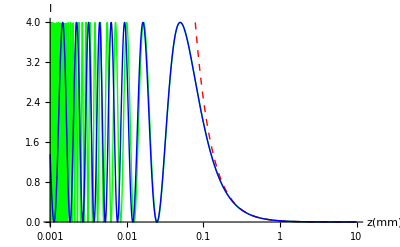

```mathematica
LogLinearPlot[{Abs[fresnel]^2/.{ℓ->10*^-3,λ->500*^-6,k->2π/(500*^-6),E0->1},Abs[fraun]^2/.{ℓ->10*^-3,λ->500*^-6,k->2π/(500*^-6),E0->1},eq103/.{ℓ->10*^-3,λ->500*^-6,k->2π/(500*^-6),E0->1}},{z,10^-3,10},PlotRange->{0,4},AxesLabel->{"z(mm)","I"},PlotStyle->{{Thin,Green},{Red,Dashed},{Blue}},PlotLegend->{"Fresnel Approx","Franhauffer Approx","Fresnel-Kirchoff"},LegendPosition->{.15,.011}]
```

### 10.9

E(x’,y’,0)= Piecewise[{{E_0 Cos[x'/L], =L/2<x'<L/2}, {0, else}}]

Fraunhoffer Approx formula from equation sheet is: E(x,y,z) = -(ⅈ ⅇ^ⅈkz ⅇ^(i k/(2z)(x^2+y^2)))/λz×∫∫E(x',y',0) ⅇ^(-ⅈ k/z(xx' yy'))dx'dy'
Making the substition for E(x’,y’,0) using the equation given us we have (note that the dy’ went away. Our slit is very narrow and the y direction doesn’t influence it): 
	E(x,y,z) = -(ⅈ ⅇ^ⅈkz ⅇ^(i k/(2z)(x^2+y^2)))/λz×∫_(-L/2)^(L/2) E_0 Cos[x'/L] ⅇ^(-ⅈ k/z(xx' yy'))dx'
Evaluating this where y’=0 we have:

```mathematica
Print["E(x,y,z) = - ⅈ SuperscriptBox[ⅇ, ⅈkz] SuperscriptBox[ⅇ, i FractionBox[k, 2  z] (SuperscriptBox[x, 2] + SuperscriptBox[y, 2])]' = " , e109 = (-I ⅇ^(I k z)ⅇ^(I k/(2z)(x^2))E0)/(λ z)*Integrate[Cos[π xp/L]*Exp[-I k/z(x xp)],{xp,-L/2,L/2}]//FullSimplify]
```

E(x,y,z) = - ⅈ SuperscriptBox[ⅇ, ⅈkz] SuperscriptBox[ⅇ, i FractionBox[k, 2  z] (SuperscriptBox[x, 2] + SuperscriptBox[y, 2])]' = (2 ⅈ ⅇ^((ⅈ k x^2)/(2 z)+ⅈ k z) E0 L π z cos((k L x)/(2 z)))/(k^2 L^2 x^2 λ-π^2 z^2 λ)

See Handwritten page for work from here.

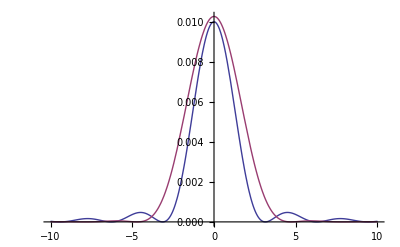

```mathematica
Plot[{0.01 Sinc[q]^2,Cos[q]^2/((π^2-4 q^2)^2)},{q,-10,10}]
```

These two plots are very similar. The blue plot is a sinc function squared-the intensity output from a single slit. As in teh single slit, if you increase the diameter of the slit you will have sharper, narrower peaks.

### Colton 5

Use the convolution theorem to find the (1D) Fourier transform of the aperture functions for 3 slits, 4 

slits, and 5 slits. The slits all have width “a”, are separated by a distance “d” (from center to center), 

and are symmetric about the origin. You can ignore factors of  √(2π) that arise from the convolution 

theorem. Hint: We did this for 2 slits in class. Use the same method. Make plots of your results for 

some “friendly” choice of parameters (ka/z=1, d=2a || 4a).

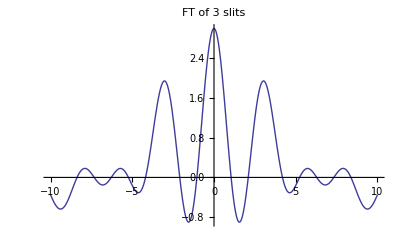

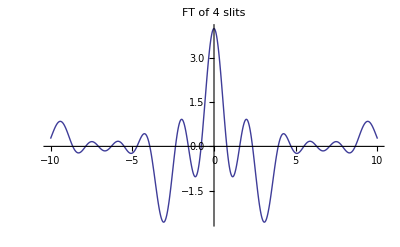

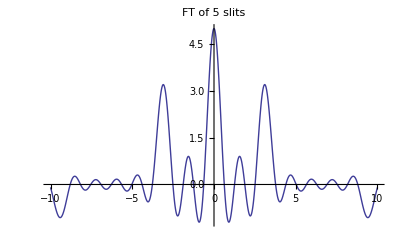

```mathematica
Plot[(Sinc[x/2]*(2Cos[2 x]+1))^1,{x,-10,10},PlotLabel->"FT of 3 slits",PlotRange->All]
Plot[(Sinc[x/2]*(2Cos[ x]+2Cos[3 x]))^1,{x,-10,10},PlotRange->All,PlotLabel->"FT of 4 slits"]
Plot[(Sinc[x/2]*(2Cos[ 2 x]+2Cos[4 x]+1))^1,{x,-10,10},PlotRange->All,PlotLabel->"FT of 5 slits"]
```

### P 11.7

I do not expect I_peakto be the same value because it is realted to a Fourier Transform. In a FT transform putitng more slits will make the transform space narrower and taller (I_peak is larger) as you add more slits.

```mathematica
ns = {1,2,5,1000}; z = 1;Δx = 5*^-6;h = 2 Δx; λ = 500*^-9;
```

Equation 11.28: I(x) = I_peak sinc^2((π Δx)/λz x) (sin^2(N (πh x)/λz))/(N^2 sin^2((πh x)/λz))

```mathematica
i117[x_,n_]:=Sinc[(π Δx)/(λ z)x]^2*Sin[n*π h x/(λ z)]^2/(n^2 Sin[π h x/(λ z)]^2)
```

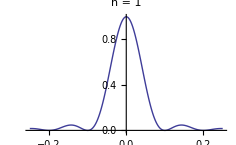
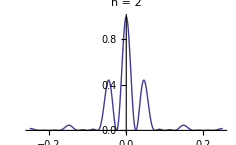
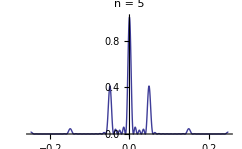
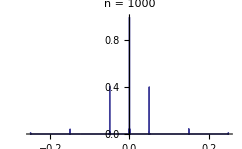

```mathematica
Table[Plot[i117[x,ns[[i]]],{x,-.25,.25},PlotPoints->500,PlotRange->All,PlotLabel->"n = "<>ToString[ns[[i]]]],{i,1,Length[ns]}]
```

## Review 3

### R68

#### a.) Derive Snell’s Law using Fermat’s principle

#### b.) Derive the Law of Reflection using Fermat’s Principle

### R69

#### a.) Consider a ray of light emitted from an object, which travels a distance d_0 before traversing a lens of focal length f and then traveling a distance d_i. Write a vector equation relating [y_2 θ_2] to [y_1 θ_1] . Be sure to simplify the equatino so that only one ABCD matric is involved. Hint: [1 | 0 -1/f | 1], [1 | d 0 | 1]

#### b.) Explain the requirement on the ABCD matrix in part (a) that ensures that an image appears for the distances chosen. From this requirement, extract a familiar constraint on d_0 and d_i. Also, make a reasonable definition for magnification M in terms of y_1 and y_2, then substitute to find M in terms of d_0 and d_i.

#### c.) A telescope is formed with two thin lenses separated by the sum of their focal lengths f_1 and f_2. Rays from a given far-away point all strike the first lens with essentially the same angle θ_1. Angular magnification M_θ quantifies the telescope’s purpose of enlarging the apparent angle between points in the field of view. Give a sensible definition for angular magnification in terms of θ_1 and θ_2. Use ABCD-matrix formulation to derive the angular magnification of the telescope in terms of f_1 and f_2.

#### R70

#### a.) Show that a system represented by a matrix [A | B C | D] (beginning and ending in the same index of refraction) can be made to look like the matrix for a thin lens if the beginning and ending positions along the z-axis are referenced from two principal planes, located distances p_1 and p_2 before and after the system. Hint: |A | B C | D| = 1

#### b.) Where are the principal planes located and what is the effective focal length for two identical thin lenses with focal lengths f that are separated by a distance d = f (see Fig. 12.12)?

### R71 Derive the on-axis intensity (i.e. x, y = 0) of a Gaussian laser beam if you know that at z = 0 the electric field of the beam is E(ρ’, z=0) = E_0 ⅇ^((-(ρ')^2)/w_0^2) Fresnel: E(x,y,d) ≃- (ⅈⅇ^(ⅈ k d)ⅇ^(ⅈ k/(2d)(x^2+y^2)))/(λ d)∫∫E(x', y', 0) ⅇ^(ι k/(2d)((x')^2+(y')^2))ⅇ^(-ⅈ k/d(x x' + y y'))ⅆx' ⅆy' ∫_(-∞)^∞ e^(-Ax^2+Bx+C) ⅆx = √(π/A)ⅇ^(B^2/(4A)) + C

### R72

#### a.) You decide to construct a simple laser cavity with a flat mirror and another mirror with concave curvature of R = 100 cm. What is the longest possible stable cavity that you can make? Hint, Sylvester’s theorem is [A | B C | D]^N = 1/(sin θ)[A sin Nθ - sin(N-1)θ | B sin Nθ C sin Nθ | D sin Nθ - sin(N-1)θ] Where cos θ = 1/2(A + D)

#### b.) The amplifier is YLF crystal, which lases at λ = 1054 nm. You decide to make the cavity 10 cm shorter than the longest possible (i.e. found in part (a)). What is the value of w0, and where is the beam waist located inside the cavity (the place we assign to z = 0)? HINT: One can interpret the parameter R (z) as the radius of curvature of the wave front. For a mode to exist in a laser cavity, the radius of curvature of each of the end mirrors must match the radius of curvature of the beam at that location. E(ρ,Z) = E_0 ω_0/(ω(z))ⅇ^(-ρ^2/(ω^2(z)))ⅇ^(ⅈkz _ ⅈ kρ^2/(2 R(z)))ⅇ^(-ⅈ tan^-1 z/z_0) ρ^2 = x^2+y(.10)^2 ω(z) = ω_0 √(1+z^2/z_0^2) R(z) = z+z_0^2/z z_0 = (k ω_0^2)/2

### R73

#### a.) Compute the Fraunhofer diffraction intensity pattern for a uniformly illuminated circular aperture with diameter l. Hint: E(x,y,d) ≃- (ⅈⅇ^(ⅈ k d)ⅇ^(ⅈ k/(2d)(x^2+y^2)))/(λ d)∫∫E(x', y', 0) ⅇ^(-ⅈ k/d(x x' + y y'))ⅆx' ⅆy' J_0(α) = 1/(2 π)∫_0^(2 π) ⅇ^(±ii α *cos(θ - θ'))ⅆθ' ∫_0^a J_0(bx)xⅆx = a/b J_1(ab) J_1(1.22 π)=0 x→^lim 0 2(J_1(x))/x=1

#### b.) The first lens of a telescope has a diameter of 30 cm, which is the only place where light is clipped. You wish to use the telescope to examine two stars in a binary system. The stars are approximately 25 light-years away. How far apart need the stars be (in the perpendicular sense) for you to distinguish them in the visible range of λ = 500 nm? Compare with the radius of Earth’s orbit, 1.5 × 108 km.

### R74

#### a.) Derive the Fraunhofer diffraction pattern for the field from a uniformly illuminated single slit of width Δx. (Don’t worry about the y -dimension.)

#### b.)Find the Fraunhofer intensity pattern for a grating of N slits of width \[Laplace]x positioned on the mask at x'_n = h(n - (N+1)/2) so that the spacing between all slits is h. Hint: The array theorem says that the diffraction pattern is ∑_(n=1)^N ⅇ^(-ⅈ k/d xx'_n)times the diffraction pattern of a single slit. You will need ∑_(n=1)^N r^n= (r^N-1)/(r-1)

#### c.) Consider Fraunhofer diffraction from the grating in part (b). The grating is 5.0 cm wide and is uniformly illuminated. For best resolution in a monochromator with a 50 cm focal length, what should the width of the exit slit be? Assume a wavelength of λ = 500 nm.

### R75

#### a.) A monochromatic plane wave with intensity I_0 and wavelength λ is incident on a circular aperture of diameter l followed by a lens of focal length f . Write the intensity distribution at a distance f behind the lens.

#### b.) You wish to spatially filter the beam such that, when it emerges from the focus, it varies smoothly without diffraction rings or hard edges. A pinhole is placed at the focus, which transmits only the central portion of the Airy pattern (inside of the first zero). Calculate the intensity pattern at a distance f after the pinhole using the approximation given in the hint below. Hint:A reasonably good approximation of the transmitted field is thatofaGaussian E(ρ,0) =E_f ⅇ^(-ρ^2/ω_0^2) whereEf isthemagnitudeof the field at the center of the focus found in part (a), and the width is w0 = 2 λf^#/π and f^# ≡ f /ℓ. The figure below shows how well the Gaussian approximation fits the actual curve. We have assumed that the first aperture is a distance f before the lens so that at the focus after the lens the wave front is flat at the pinhole. To avoid integration, you may want to use the result of P11.12 or P11.11(b) to get the Fraunhofer limit of the Gaussian profile. (See figure below.)

## 22 - Due late

## 23 -Due late

### P11.5

```mathematica
kOverd = 1; a = 1; b = 5;
```

```mathematica
plot115 [x_,y_]:=(BesselJ[1,kOverd*a*√(x^2+y^2) ]/(kOverd*a*√(x^2+y^2)))^2 * ( 1+ Cos[b x kOverd])^2* ( 1+ Cos[b y kOverd])^2
```

```mathematica
GraphicsGrid[{{Plot3D[plot115[x,y],{x,-5,5}, {y,-5,5},PlotRange->{0,10},PlotPoints->100],Plot3D[plot115[x,y],{x,-5,5}, {y,-5,5},PlotRange->{0,5},PlotPoints->100]},{Plot3D[plot115[x,y],{x,-10,10}, {y,-10,10},PlotRange->{0,.5},PlotPoints->100],Plot3D[plot115[x,y],{x,-10,10}, {y,-10,10},PlotRange->{0,.1},PlotPoints->100]}}]
```

-Graphics-

### Colton 8

```mathematica
a8 = 1; b8 = 1; d8 = 3; L8 = 3; kOverd8 = 1;
```

```mathematica
partA[x_,y_]:=(2 π b8^2 BesselJ[1, kOverd8*√(x^2+y^2)]/(√(x^2+y^2)*kOverd8) - 2 a8^2 Sinc[kOverd8 x/2]*Sinc[kOverd8 y/2])^2
```

```mathematica
partB[x_,y_]:=(16 π^2 b8^4*BesselJ[1,b8 √(x^2+y^2)kOverd]^2 Sin[d8 x kOverd8]^2)/(x^2+y^2 b8^2 kOverd^2)
```

```mathematica
partC[x_,y_]:=partA[x,y]+partB[x,y] +8 π b8^2(BesselK[1, √(x^2+y^2)b8 kOverd8]/(√(x^2+y^2)b8 kOverd8))*Sin[d8 x kOverd8]*Sin[d8 y kOverd8]*(2π b8^2(BesselJ[1,kOverd8 * √(x^2+y^2)b8])/(√(x^2+y^2)kOverd8 8 b8) - 2Sinc[x kOverd8 a8/2]*Sinc[y kOverd8 a8/2])
```

```mathematica
GraphicsGrid[
{
{Plot3D[partA[x,y],{x,-16,16},{y,-16,16},PlotRange->{0,40},PlotPoints->50,PlotLabel->"Part a: Range {0,40}"],
Plot3D[partA[x,y],{x,-16,16},{y,-16,16},PlotRange->{0,6},PlotPoints->50,PlotLabel->"Part a: Range {0,6}"],
Plot3D[partA[x,y],{x,-16,16},{y,-16,16},PlotRange->{0,1},PlotPoints->50,PlotLabel->"Part a: Range {0,1}"],
Plot3D[partA[x,y],{x,-16,16},{y,-16,16},PlotRange->{0,.2},PlotPoints->50,PlotLabel->"Part a: Range {0, .2}"]},


{Plot3D[partB[x,y],{x,-16,16},{y,-16,16},PlotRange->{0,40},PlotPoints->50,PlotLabel->"Partb b: Range {0,40}"],
Plot3D[partB[x,y],{x,-16,16},{y,-16,16},PlotRange->{0,6},PlotPoints->50,PlotLabel->"Part b: Range {0,6}"],
Plot3D[partB[x,y],{x,-16,16},{y,-16,16},PlotRange->{0,1},PlotPoints->50,PlotLabel->"Part b: Range {0,1}"],
Plot3D[partB[x,y],{x,-16,16},{y,-16,16},PlotRange->{0,.2},PlotPoints->50,PlotLabel->"Part b: Range {0, .2}"]},


{Plot3D[partC[x,y],{x,-16,16},{y,-16,16},PlotRange->{0,40},PlotPoints->50,PlotLabel->"Part c: Range {0,40}"],
Plot3D[partC[x,y],{x,-16,16},{y,-16,16},PlotRange->{0,6},PlotPoints->50,PlotLabel->"Part c: Range {0,6}"],
Plot3D[partC[x,y],{x,-16,16},{y,-16,16},PlotRange->{0,1},PlotPoints->50,PlotLabel->"Part c: Range {0,1}"],
Plot3D[partC[x,y],{x,-16,16},{y,-16,16},PlotRange->{0,.2},PlotPoints->50,PlotLabel->"Part c: Range {0, .2}"]}
}
]
```

-Graphics-

## 25 - Due 4-10-12

### P13.4

#### a.)

```mathematica
ρ[λ_]:=(8 h c π)/(λ^5*(Exp[h c/(λ k T)]-1))
```

```mathematica
D[ρ[λ],λ]
```

(8 π c^2 h^2 ⅇ^((c h)/(k λ T)))/(k λ^7 T (ⅇ^((c h)/(k λ T))-1)^2)-(40 π c h)/(λ^6 (ⅇ^((c h)/(k λ T))-1))

#### b.)

```mathematica
λmax = .0029/5750
```

5.04348×10^-7

#### c.)

```mathematica
ρω[ω_]:=(ℏ ω^3)/(π^2 c^3*(Exp[ℏ ω /(k T)] - 1))
```

```mathematica
D[ρω[ω],ω]
Quiet[Solve[D[ρω[ω],ω]==0,ω]]//N
```

(3 ω^2 ℏ)/(π^2 c^3 (ⅇ^((ω ℏ)/(k T))-1))-(ω^3 ℏ^2 ⅇ^((ω ℏ)/(k T)))/(π^2 c^3 k T (ⅇ^((ω ℏ)/(k T))-1)^2)

{{ω→(2.82144 k T)/ℏ}}

```mathematica
ωmax = 2.82144 * 1.380*^-23 * 5750/6.626*^-34
νmax = ωmax/(2π)
```

3.37883×10^14

5.37757×10^13

```mathematica
3*^8/λmax
```

5.94828×10^14

### Colton 11

#### a.)

```mathematica
rsun = 6.96*^8; σ = 5.67*^-8;
```

```mathematica
power= σ *5750^4*4π rsun^2
```

3.77297×10^26

#### b.)

```mathematica
rearth = AstronomicalData["Earth","EquatorialRadius"];
rorbit = AstronomicalData["Earth", "SemimajorAxis"];
areaDisk = π rearth^2;
areaSphere = 4 π rorbit^2;
powerEarth = areaDisk/areaSphere*power
```

1.71459×10^17

#### c.)

```mathematica
(powerEarth/(4 π rearth^2*σ))^(1/4)-273.15
```

4.17865

### Colton 12

#### a.)

```mathematica
pradiated = σ*(33+273.15)^4*.97*1.4
pabsorbed = σ (20+273.15)^4*.97*1.4
pnet = pradiated-pabsorbed
```

676.425

568.647

107.779

#### b.)

```mathematica
λmax12 = 0.0029/(33+273.15)
```

9.47248×10^-6

### Colton 13

#### b.)

```mathematica
ans =DSolve[{x'[t] + 1/τ1*x[t] - 1/τ2 y[t]==0,y'[t]+1/τ2*y[t]-P2==0,y[0]==0,x[0]==0},{x[t],y[t]},t];
N1[t_]:=x[t]/.ans[[1,1]]
N2[t_]:=y[t]/.ans[[1,2]]
```

```mathematica
N1[t]//FullSimplify
N2[t]//FullSimplify
```

(P2 τ1 (τ1 (-ⅇ^(-t/τ1))+τ2 (ⅇ^(-t/τ2)-1)+τ1))/(τ1-τ2)

P2 τ2 (1-ⅇ^(-t/τ2))

#### c.)

```mathematica
τ1 = 2*10^-6; τ2 = 1*10^-6;P2 = 10^20;
```

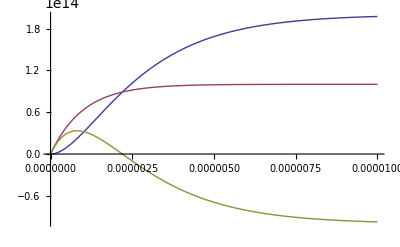

N_2-N_1>0   ∀   t >0

```mathematica
Plot[{N1[t],N2[t],N2[t]-N1[t]},{t,0,.00001}]
Print[" N_2-N_1>0   ∀   t >0"]
```

#### d.)

```mathematica
Print["The steady state for N_2[t] = ",N1[t]/.t->100//N,"  And the steady state for N_2[t] = ", N2[t]/.t->100//N]
Print["This means a population inversion happens and there is potential for lasing"]
```

The steady state for N_2[t] = 2.×10^14  And the steady state for N_2[t] = 1.×10^14

This means a population inversion happens and there is potential for lasing

## 26 - Due 4-11-12

#### d and e.)

As can be seen above, my color doesn’t lie in the sRBG color gamut and therefore cannot be shown in that system.

### Colton 15

#### a, d.)

#### b.)

For point A we have to use the complementary wavelength for the hue and it looks like that is λ_c ≈ 508 nm
saturation ≈ .62

#### c.)

For point B we get λ_d≈ 570 nm
saturation ≈ .78.

#### d.)

The chromaticity can be seen with the dotted lines in the diagram above and it is, predictably (.45,.3). I say this is predictable because that is just the average value of the two (x,y) pairs.

#### e.)

```mathematica
.6*(14/15)
.4*(14/15)
1/15.
```

0.56

0.373333

0.0666667

### P2.13

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
colorFunction = Transpose[Import["colorfunctions.csv"]];
list1 = Transpose[{colorFunction[[1]],colorFunction[[2]]}];
list2 = Transpose[{colorFunction[[1]],colorFunction[[3]]}];
list3 = Transpose[{colorFunction[[1]],colorFunction[[4]]}];
```

```mathematica
xx[λ_]:=  Interpolation[list1,λ];
yy[λ_]:= Interpolation[list2,λ];
zz[λ_]:=  Interpolation[list3,λ];
```

```mathematica
Intensity[λ_]:=Exp[- ((λ - 500)/20)^2]
```

```mathematica
X = NIntegrate[Intensity[λ]*xx[λ],{λ,360,830}];
Y = NIntegrate[Intensity[λ]*yy[λ],{λ,360,830}];
Z = NIntegrate[Intensity[λ]*zz[λ],{λ,360,830}];
Print["X = ",X, "    Y = ",Y, "    Z=",Z]
```

X = 1.45656    Y = 13.1099    Z=12.6078